```mathematica
Clear[ rcap, scap ] ;
rcap = {Cos[#], Sin[#]} & ;
scap = {Sin[#1] Cos[#2], Sin[#1] Sin[#2], Cos[#1]} & ;
(*rcap[θ]
scap[θ, ϕ]*)

asz = 1.5 ;
toff = 0.1 ;
axes = Graphics3D[{
Red,Arrow[Tube[{{0,0,0},{asz,0,0}}] , 0.05],
Blue,Arrow[Tube[{{0,0,0},{0,asz,0}}] , 0.05],
Darker[Green, .8],Arrow[Tube[{{0,0,0},{0,0,asz}}] , 0.05],
Text[ "e_1",  {asz + toff,0,0} ],
Text[ "e_2",  {0,asz + toff,0} ],
Text[ "e_3",  {0,0,asz + toff} ]
}] ;
```

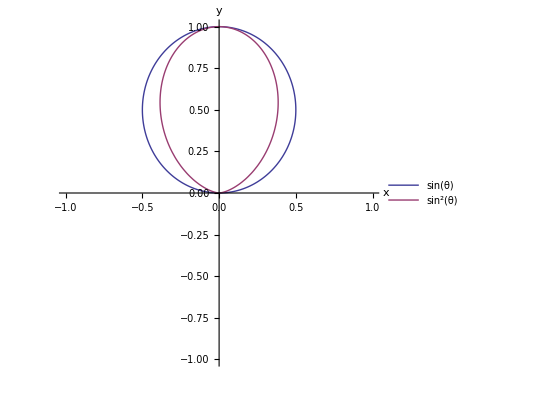

-Graphics3D-

-Graphics3D-

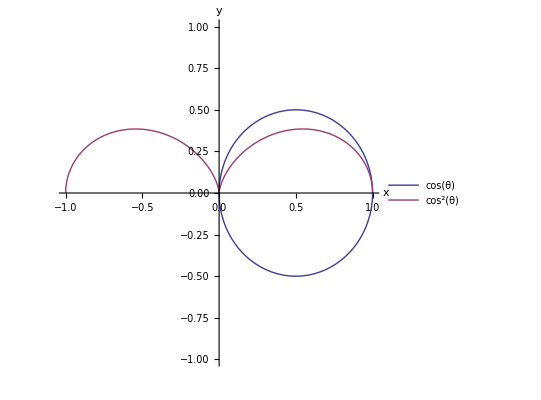

-Graphics3D-

-Graphics3D-

```mathematica
(*x1 = With[{funcList={Sin[t]rcap[t], Sin[t]^2rcap[t]},
labelList = {"sin(θ)", "sin^2(θ)"}
},With[{n=Length@funcList},Legended[ParametricPlot[funcList,{t, 0, Pi}, PlotRange -> {-1, 1}, AxesLabel -> {x, y}],LineLegend[(ColorData[1][#])&/@#,labelList[[#]]]&@Range@n]]
]*)
(*p1 = ParametricPlot[{Sin[t]rcap[t], Sin[t]^2rcap[t]}, {t, 0, Pi}, PlotRange -> {-1, 1}, AxesLabel -> {x, y}
,PlotLegends->Placed[{"sin(θ)", "sin^2(θ)"},{Right,Bottom}]
]*)
(*y1=With[{funcList={Sin[t] rcap[t],Sin[t]^2 rcap[t]},labelList={"sin(θ)", "sin^2(θ)"}},With[{n=Length@funcList},ParametricPlot[funcList,{t,0,Pi},PlotRange->{-1,1},AxesLabel->{x,y},PlotLegends->Placed[LineLegend[ColorData[1][#]&/@Range@n,labelList[[Range@n]]],{Right,Bottom}]]]]*)
(*http://mathematica.stackexchange.com/a/72045/10*)
p1=With[{funcList={Sin[t] rcap[t],Sin[t]^2 rcap[t]},labelList={"sin(θ)", "sin^2(θ)"}},With[{n=Length@funcList},Legended[ParametricPlot[funcList,{t,0,Pi},PlotRange->{-1,1},AxesLabel->{x,y}],Placed[LineLegend[(ColorData[1][#])&/@#,labelList[[#]]]&@Range@n,{Right,Bottom}]]]]
(*x1 = Plot[{Sin[t], Sin[t]^2}, {t, 0, Pi}, PlotRange -> {-1, 1}, AxesLabel -> {x, y}
,PlotLegends->Placed[{"sin(θ)", "sin^2(θ)"},{Right,Bottom}]
]*)

s1 = Show[axes,ParametricPlot3D[ {Sin[t]scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}]]
s2 = Show[axes,ParametricPlot3D[ {Sin[t]^2scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}]]

(*p2 = ParametricPlot[{Cos[t]rcap[t], Cos[t]^2rcap[t]}, {t, 0, Pi}, PlotRange -> {-1, 1}, AxesLabel -> {x, y}]*)
p2=With[{funcList={Cos[t] rcap[t],Cos[t]^2 rcap[t]},labelList={"cos(θ)", "cos^2(θ)"}},With[{n=Length@funcList},Legended[ParametricPlot[funcList,{t,0,Pi},PlotRange->{-1,1},AxesLabel->{x,y}],Placed[LineLegend[(ColorData[1][#])&/@#,labelList[[#]]]&@Range@n,{Right,Bottom}]]]]
s3 = Show[axes,ParametricPlot3D[ {Cos[t]scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}]]
s4 = Show[axes,ParametricPlot3D[ {Cos[t]^2scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}]]
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "figures/ece1229" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229

```mathematica
peeters`exportForLatex["SineAndSinSq", p1]
peeters`exportForLatex["CoSineAndCoSineSq", p2]
peeters`exportForLatex["SineSq3D", s2]
peeters`exportForLatex["CoSineSq3D", s4]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/SineSq3D.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/SineSq3Dpn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/CoSineSq3D.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/CoSineSq3Dpn.png}

```mathematica
t1 = Show[axes,ParametricPlot3D[ { (Cos[t]^2 Cos[p]^2 + Sin[p]^2)scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}]]
t2 = Show[axes,ParametricPlot3D[ { ((*Cos[t]^2 Cos[p]^2 +*) Sin[p]^2)scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}]]
t3 = Show[axes,ParametricPlot3D[ { (Cos[t]^2 Cos[p]^2 (*+ Sin[p]^2*))scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
peeters`exportForLatex["TaiAndPereiraSampleFieldThetaCapComponentFig1", t3]
peeters`exportForLatex["TaiAndPereiraSampleFieldPhiCapComponentFig2", t2]
peeters`exportForLatex["TaiAndPereiraSampleFieldAllComponentsFig3", t1]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/TaiAndPereiraSampleFieldAllComponentsFig3.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/TaiAndPereiraSampleFieldAllComponentsFig3pn.png}